```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
FileExport[data_, filename_?StringQ,c_?NumberQ,h_?NumberQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic",StringJoin["c=",ToString@c], StringJoin["h=",ToString@h]}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
metadata = Import["metadata.json"]/.Rule-> List
```

{{grid,{{space,{{a,10.0},{b,200.0},{h,1.0},{n,189}}},{time,{{a,0.0},{b,200.0},{h,0.8},{n,249}}}}},{norms,{{C,Null},{L,Null},{L2,0.024774613444289086},{W2,Null}}},{profile,cos},{scheme,advectionPPML},{speed,1},{type,Advection}}

```mathematica
time = ToExpression@Table[metadata⟦1,2,2,2,i,2⟧, {i, 1, 4}]
```

{0.,200.,0.8,249}

```mathematica
space= ToExpression@Table[metadata⟦1,2,1,2,i,2⟧, {i, 1, 4}]
```

{10.,200.,1.,189}

```mathematica
norms = ToExpression@Table[metadata⟦2,2,i,2⟧, {i, 1, 4}]
```

{Null,Null,0.0247746,Null}

```mathematica
profile = metadata⟦3, 2⟧
```

cos

```mathematica
c = ToExpression@metadata⟦5,2⟧
```

1

```mathematica
Subscript[l, 1] = space[[1]];
Subscript[l, 2] = 30;
Subscript[l, 11] = 50/3;
Subscript[l, 12] = 20;
Subscript[l, 22]= 70/3;
L = space⟦2⟧;
T = time[[2]];
```

```mathematica
Profile[profile_?StringQ]:= Which[
profile == "leftTriangle", Piecewise[{{0, x < Subscript[l, 1]}, {1/(Subscript[l, 2]-Subscript[l, 1])(x-Subscript[l, 1]), x>= Subscript[l, 1]&& x<= Subscript[l, 2]}, {0, x>Subscript[l, 2]}}],
profile == "rightTriangle", Piecewise[{{0, x < Subscript[l, 1]}, {1/(Subscript[l, 2] -Subscript[l, 1])(Subscript[l, 2]-x), x>= Subscript[l, 1]&& x<= Subscript[l, 2]}, {0, x>Subscript[l, 2]}}] ,
profile == "rectangle",Piecewise[{{0, x < Subscript[l, 1]}, {1, x>= Subscript[l, 1]&& x<= Subscript[l, 2]}, {0, x>Subscript[l, 2]}}],
profile == "cos",Piecewise[{{0, x < Subscript[l, 1]}, {1/2-1/2 Cos[(2 π)/(Subscript[l, 2] - Subscript[l, 1])(x-Subscript[l, 1])], x>= Subscript[l, 1]&& x<= Subscript[l, 2]}, {0, x>Subscript[l, 2]}}] ,
profile == "tooth", Piecewise[{{0, x<Subscript[l, 1]},{-2/(3(Subscript[l, 11] - Subscript[l, 1]))(x-Subscript[l, 1]) + 1, x>Subscript[l, 1]&&x< Subscript[l, 11]}, {1/3, x>= Subscript[l, 11]&&x<= Subscript[l, 22]},{2/(3(Subscript[l, 2]-Subscript[l, 22]))(x-Subscript[l, 2]) + 1, x >Subscript[l, 22] && x<= Subscript[l, 2]}, {0, x> Subscript[l, 2]} }],
profile == "m", Piecewise [{ {0, x< Subscript[l, 1]}, { -2/(3(Subscript[l, 12] - Subscript[l, 1]))(x-Subscript[l, 1]) + 1, x>= Subscript[l, 1]&&x < Subscript[l, 12]}, {2/(3(Subscript[l, 2]-Subscript[l, 12]))(x-Subscript[l, 2])+1, x >= Subscript[l, 12]&& x<=Subscript[l, 2]}, {0, x >Subscript[l, 2]} }]
]
```

```mathematica
selectedProfile = Profile[profile];
```

```mathematica
func[t_]:= selectedProfile/.x-> t
```

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return[solution]
];
```

```mathematica
Plots[data_List]:=Module[{list, plot, timestamps},
timestamps = #⟦1⟧ &/@ data;
plot=Plot[func[χ-c*#], {χ, Subscript[l, 1], L}, PlotStyle-> {Black, Thickness -> 0.0005}]&/@timestamps;
list = ListPlot[#⟦2⟧ &/@ data];
Return@Show[Show[plot], list, ImageSize->700, PlotRange-> All, LabelStyle-> Directive[Black, FontFamily-> "Times", 16]]
];
```

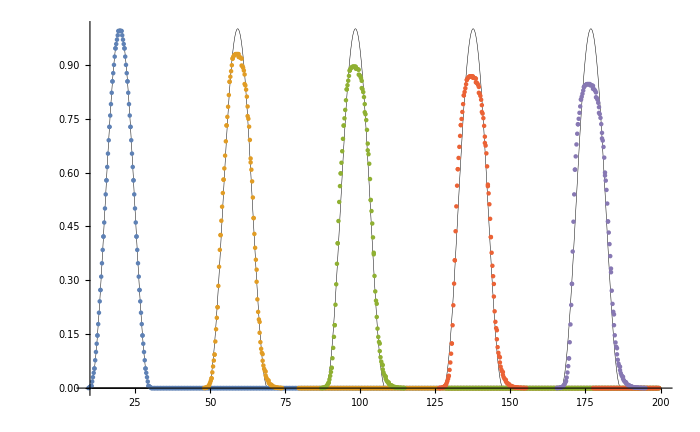

```mathematica
advectionPPM = NormalRepresentation@Import["advectionPPM.json"] ;
ppmPlot =Plots[advectionPPM]
```

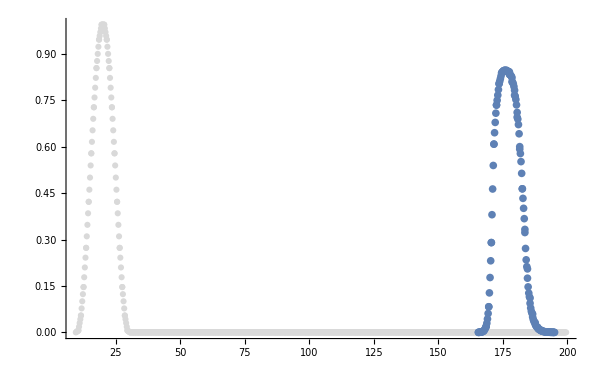

```mathematica
Show[ListPlot[advectionPPM⟦1,2⟧, PlotStyle->LightGray],ListPlot[advectionPPM⟦5,2⟧], ImageSize->600, PlotRange-> All]
```

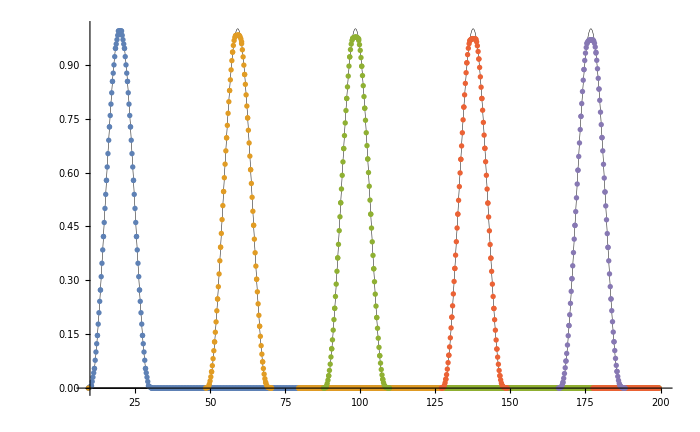

```mathematica
advectionPPML = NormalRepresentation@Import["advectionPPML.json"] ;
ppmlPlot = Plots[advectionPPML]
```

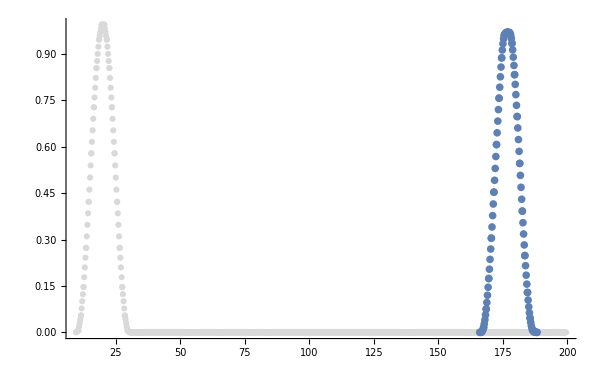

```mathematica
Show[ListPlot[advectionPPML⟦1,2⟧, PlotStyle->LightGray],ListPlot[advectionPPML⟦5,2⟧], ImageSize->600, PlotRange-> All]
```

```mathematica
If[!True ,
FileExport[ppmPlot, StringJoin["advectionPPM_", profile,".pdf"],c,space⟦3⟧, "PDF"];
FileExport[ppmlPlot, StringJoin["advectionPPML_", profile,".pdf"],c,space⟦3⟧, "PDF"];
];
```